# Parser

Parser for the grammar:

## Recursive descent parser

```mathematica
MapUntilArg[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[#[[2,1]]] && Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapWhileArg[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1]}&,
{0,expr},
test[#[[2,1]]]&
][[All,1]],
1];
```

```mathematica
MapUntil[f,Range[5],#=!=$Failed&]
```

{$Failed,2}

```mathematica
MapUntil[f,Range[5],#===7&]
```

{$Failed,2,3,4,5}

```mathematica
Protect[EmptyString,Term,NonTerm];

Match[input_,terms_]:=(Take[input,Length[terms]] == terms);
GetArgument[_[arg_]]:=arg;

MatchTerminalsWithRule[input_,rule_]:=Block[{terms,rest,matched,cuttedInput,currentState = rule["From"]},
If[rule["To"]===EmptyString,Return[{{currentState->EmptyString},{},input}]];

terms = MapWhileArg[GetArgument,rule["To"],Head[#]=!=NonTerm&];
rest = Drop[rule["To"],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[Match[input,terms],
matched = Thread[currentState->terms];
cuttedInput = Drop[input,Length[terms]];
Return[{matched,rest,cuttedInput}];
,
Return[$Failed];
];
];

MatchTerminals[state_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[MatchTerminalsWithRule[input,#]&,possibleTransitions,#=!=$Failed&]];
Return[matched];
];
```

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
MatchTerminals["E'",{"+","i","$"},grammar]
```

{{E'→+,E'→i},{NonTerm[E']},{$}}

Parse

```mathematica
AddDepthToSingleRule[n_,Rule[a_,b_]]:=Rule[{n,a},{n,b}];
AddDepthToRules[n_,rules_]:=Map[AddDepthToSingleRule[n,#]&,rules];
StackSymbols[caller_,depth_,list_]:=Map[<|"Caller"->caller,"Depth"->depth,"Symbol"->#|>&,list];

Parse[input_,grammar_]:=Block[{start,inputBuffer,enter,parseTree,stack,transitions,next,depth},
start = First[grammar]["From"];
inputBuffer = Characters[input];

enter = start;
parseTree = {};
stack ={};
depth = 0;

While[{inputBuffer,enter} =!= {{"$"},None},

{transitions,next,inputBuffer}=MatchTerminals[enter,inputBuffer,grammar];
AppendTo[parseTree,AddDepthToRules[depth,transitions]];

If[Length[next] > 0,
AppendTo[parseTree,{depth,enter}->{depth+1,First[next]}];
{enter,stack} ={First[next],Join[stack,StackSymbols[enter,depth,Rest[next]]]};
depth++;
,
If[Length[stack] > 0,
AppendTo[parseTree,{Last[stack]["Depth"],Last[stack]["Caller"]}->{Last[stack]["Depth"]+1,Last[stack]["Symbol"]}];
depth = Last[stack]["Depth"]+1;
{enter,stack} = {Last[stack]["Symbol"],Drop[stack,-1]};
,
enter = None;
]
]
];

Return[Flatten[parseTree,1]];

];
```

```mathematica
Parse["i+i+ijj$",grammar]
```

{{0,NonTerm[E]}→{0,i},{0,NonTerm[E]}→{1,NonTerm[E']},{1,NonTerm[E']}→{1,+},{1,NonTerm[E']}→{1,i},{1,NonTerm[E']}→{2,NonTerm[E']},{2,NonTerm[E']}→{2,+},{2,NonTerm[E']}→{2,i},{2,NonTerm[E']}→{3,NonTerm[E']},{3,NonTerm[E']}→{3,EmptyString},{0,NonTerm[E]}→{1,NonTerm[V]},{1,NonTerm[V]}→{1,j},{1,NonTerm[V]}→{2,NonTerm[V]},{2,NonTerm[V]}→{2,j},{2,NonTerm[V]}→{3,NonTerm[V]},{3,NonTerm[V]}→{3,EmptyString}}

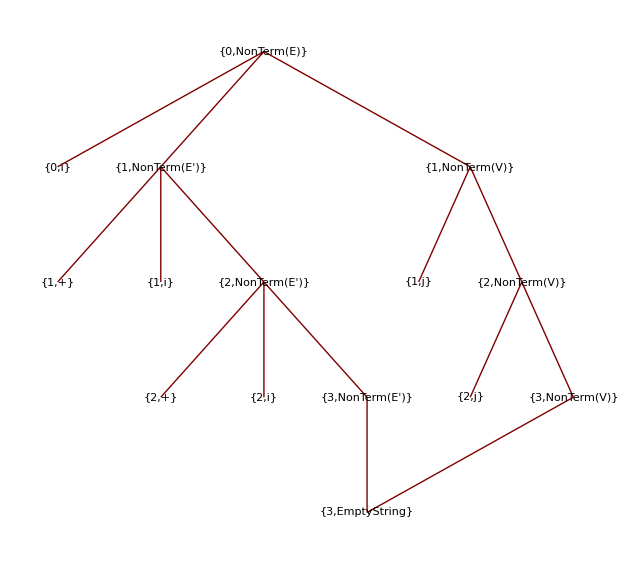

```mathematica
TreePlot[Parse["i+i+ijj$",grammar],Automatic,{0,NonTerm["E"]},VertexLabeling->True]
```